2

50

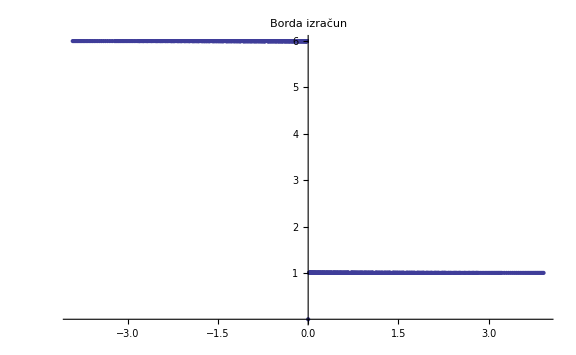

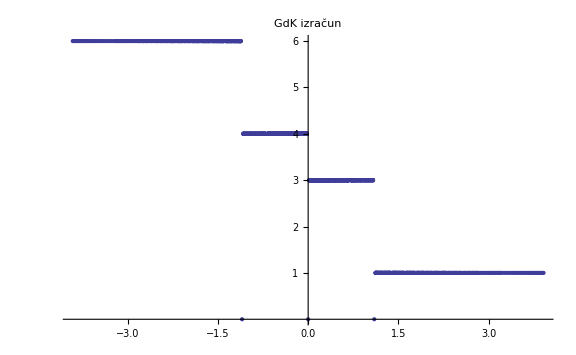

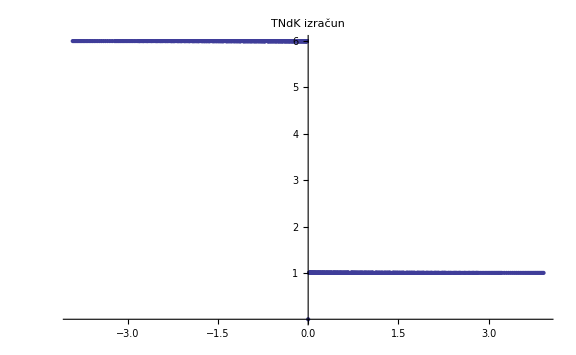

```mathematica
d=2
n=50
Borda=Table[0,{i,n},{j,n}];
GdK=Table[0,{i,n},{j,n}];
TNdK=Table[0,{i,n},{j,n}];

For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
alfa={i,0,0,0,0,j};

(*Borda*)
BoA=2*(alfa[[1]]+alfa[[4]])+alfa[[2]]+alfa[[5]];
BoB=2*(alfa[[3]]+alfa[[5]])+alfa[[1]]+alfa[[6]];
BoC=2*(alfa[[2]]+alfa[[6]])+alfa[[3]]+alfa[[4]];

Which[And[BoA>BoB,BoB>BoC],Borda[[i,j]]=1,And[BoA>BoC,BoB<BoC],Borda[[i,j]]=2,And[BoA<BoB,BoA>BoC],Borda[[i,j]]=3,And[BoA<BoC,BoB>BoC],Borda[[i,j]]=4,And[BoA>BoB,BoA<BoC],Borda[[i,j]]=5,And[BoA<BoB,BoB<BoC],Borda[[i,j]]=6, True,Borda[[i,j]]=0];



(*GdK*)
GdKA=alfa[[2]]+alfa[[5]]+(alfa[[3]]+alfa[[6]])*2^d;
GdKB=alfa[[1]]+alfa[[6]]+(alfa[[2]]+alfa[[4]])*2^d;
GdKC=alfa[[3]]+alfa[[4]]+(alfa[[1]]+alfa[[5]])*2^d;
Which[And[GdKA<GdKB,GdKB<GdKC],GdK[[i,j]]=1,And[GdKA<GdKC,GdKB>GdKC],GdK[[i,j]]=2,And[GdKA>GdKB,GdKA<GdKC],GdK[[i,j]]=3,And[GdKC>GdKB,GdKC<GdKA],GdK[[i,j]]=4,And[GdKC<GdKA,GdKA<GdKB],GdK[[i,j]]=5,And[GdKC<GdKB,GdKB<GdKA],GdK[[i,j]]=6,True,GdK[[i,j]]=0];


(*TNdK*)
MdK={{alfa[[2]]+alfa[[5]]+(alfa[[3]]+alfa[[6]])*2^d,alfa[[1]]+alfa[[3]]+alfa[[4]]+alfa[[6]],alfa[[2]]+alfa[[5]]+(alfa[[1]]+alfa[[4]])*2^d},{alfa[[1]]+alfa[[6]]+(alfa[[2]]+alfa[[4]])*2^d,alfa[[2]]+alfa[[3]]+alfa[[4]]+alfa[[5]],alfa[[1]]+alfa[[6]]+(alfa[[3]]+alfa[[5]])*2^d},{alfa[[3]]+alfa[[4]]+(alfa[[1]]+alfa[[5]])*2^d,alfa[[1]]+alfa[[2]]+alfa[[5]]+alfa[[6]],alfa[[3]]+alfa[[4]]+(alfa[[2]]+alfa[[6]])*2^d}}; 

TNdKABC=MdK[[1,1]]+MdK[[2,2]]+MdK[[3,3]];
TNdKACB=MdK[[1,1]]+MdK[[2,3]]+MdK[[3,2]];
TNdKBAC=MdK[[1,2]]+MdK[[2,1]]+MdK[[3,3]];
TNdKBCA=MdK[[1,3]]+MdK[[2,1]]+MdK[[3,2]];
TNdKCAB=MdK[[1,2]]+MdK[[2,3]]+MdK[[3,1]];
TNdKCBA=MdK[[1,3]]+MdK[[2,2]]+MdK[[3,1]];
Which[And[TNdKABC<TNdKACB,TNdKABC<TNdKBAC,TNdKABC<TNdKBCA,TNdKABC<TNdKCAB,TNdKABC<TNdKCBA],TNdK[[i,j]]=1,And[TNdKACB<TNdKABC,TNdKACB<TNdKBAC,TNdKACB<TNdKBCA,TNdKACB<TNdKCAB,TNdKACB<TNdKCBA],TNdK[[i,j]]=2,And[TNdKBAC<TNdKABC,TNdKBAC<TNdKACB,TNdKBAC<TNdKBCA,TNdKBAC<TNdKCAB,TNdKBAC<TNdKCBA],TNdK[[i,j]]=3,And[TNdKBCA<TNdKABC,TNdKBCA<TNdKACB,TNdKBCA<TNdKBAC,TNdKBCA<TNdKCAB,TNdKBCA<TNdKCBA],TNdK[[i,j]]=4,And[TNdKCAB<TNdKABC,TNdKCAB<TNdKACB,TNdKCAB<TNdKBAC,TNdKCAB<TNdKBCA,TNdKCAB<TNdKCBA],TNdK[[i,j]]=5,And[TNdKCBA<TNdKABC,TNdKCBA<TNdKACB,TNdKCBA<TNdKBAC,TNdKCBA<TNdKBCA,TNdKCBA<TNdKCAB],TNdK[[i,j]]=6,True,TNdK[[i,j]]=0];



]]

MatrixForm[Borda];
MatrixForm[GdK];
MatrixForm[TNdK];

(*CRTANJE BORDA*)
BordaRez=Table[{0,0},{i,n^2}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
BordaRez[[(i-1)*n+j,1]]=Log[i/j];
BordaRez[[(i-1)*n+j,2]]=Borda[[i,j]]
]]
BordaRez=DeleteDuplicates[BordaRez];
ListPlot[BordaRez,PlotRange->{0,6},Ticks->{Automatic,{1,2,3,4,5,6}},PlotLabel->"Borda izračun",ImageSize->Large]


(*CRTANJE GdK*)
GdKRez=Table[{0,0},{i,n^2}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
GdKRez[[(i-1)*n+j,1]]=Log[i/j];
GdKRez[[(i-1)*n+j,2]]=GdK[[i,j]]
]]
GdKRez=DeleteDuplicates[GdKRez];
ListPlot[GdKRez,PlotRange->{0,6},Ticks->{Automatic,{1,2,3,4,5,6}},PlotLabel->"GdK izračun",ImageSize->Large]

(*CRTANJE TNdK*)
TNdKRez=Table[{0,0},{i,n^2}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
TNdKRez[[(i-1)*n+j,1]]=Log[i/j];
TNdKRez[[(i-1)*n+j,2]]=TNdK[[i,j]]
]]
TNdKRez=DeleteDuplicates[TNdKRez];
ListPlot[TNdKRez,PlotRange->{0,6},Ticks->{Automatic,{1,2,3,4,5,6}},PlotLabel->"TNdK izračun",ImageSize->Large]
```